# Числено диференциране

## Създаваме табличната функция

```mathematica
a =5.;b = 6;
n = 10;
h = (b-a)/n;
xt = Table[a + i*h,{i,0,n}]
```

{5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.}

```mathematica
Length[xt]
```

11

```mathematica
f[x_]:= 4 Sin[π x - 3]
yt =f[xt]
```

{0.56448,1.76055,2.78429,3.53548,3.94059,3.95997,3.59172,2.87189,1.87094,0.686846,-0.56448}

## Намиране на производните с точност O(h) - първи порядък на грешката

### Първа производна

```mathematica
z = Table[(yt[[i+1]]-yt[[i]])/h,{i,1,n}]
```

{11.9607,10.2374,7.5119,4.05113,0.193808,-3.68249,-7.19831,-10.0095,-11.8409,-12.5133}

добавяме последния елемент

```mathematica
AppendTo[z, (yt[[n+1]]-yt[[n]])/h]
```

{11.9607,10.2374,7.5119,4.05113,0.193808,-3.68249,-7.19831,-10.0095,-11.8409,-12.5133,-12.5133}

#### Оценка на грешката

теоретична грешка

```mathematica
h
```

0.1

истинска грешка

```mathematica
z(*приближена стойност*)
```

{11.9607,10.2374,7.5119,4.05113,0.193808,-3.68249,-7.19831,-10.0095,-11.8409,-12.5133,-12.5133}

```mathematica
f'[xt](*истинска стойност*)
```

{12.4406,11.2837,9.02231,5.87773,2.15779,-1.77337,-5.53093,-8.74709,-11.107,-12.3797,-12.4406}

```mathematica
Abs[z-f'[xt]]
```

{0.479909,1.04637,1.51041,1.82659,1.96398,1.90912,1.66738,1.26243,0.733898,0.13353,0.0726438}

#### Визуализация

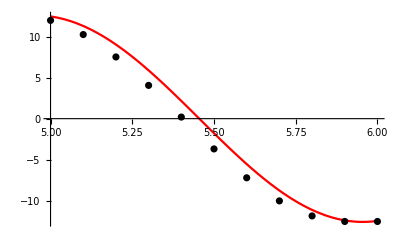

```mathematica
points = Table[{xt[[i]],z[[i]]},{i,1,n+1}];
grp = ListPlot[points,PlotStyle->Black];
grf = Plot[f'[x],{x,a,b}, PlotStyle->Red];
Show[grf, grp]
```

## Намиране на производните с точност O(h^2) - втори порядък на грешката

### Първа производна

попълваме вътрешните стойности

```mathematica
z = Table[(yt[[i+1]]-yt[[i-1]])/(2h),{i,2,n}]
```

{11.099,8.87463,5.78152,2.12247,-1.74434,-5.4404,-8.60392,-10.9252,-12.1771}

добавяме последния елемент

```mathematica
AppendTo[z, (yt[[n-1]]-4yt[[n]]+3yt[[n+1]])/(2h)]
```

{11.099,8.87463,5.78152,2.12247,-1.74434,-5.4404,-8.60392,-10.9252,-12.1771,-12.8494}

добавяме първия елемент

```mathematica
PrependTo[z, (-3yt[[1]]+4yt[[2]]-yt[[3]])/(2h)]
```

{12.8224,11.099,8.87463,5.78152,2.12247,-1.74434,-5.4404,-8.60392,-10.9252,-12.1771,-12.8494}

#### Оценка на грешката

теоретична грешка

```mathematica
h^2
```

0.01

истинска грешка

```mathematica
z(*приближена стойност*)
```

{12.8224,11.099,8.87463,5.78152,2.12247,-1.74434,-5.4404,-8.60392,-10.9252,-12.1771,-12.8494}

```mathematica
f'[xt](*истинска стойност*)
```

{12.4406,11.2837,9.02231,5.87773,2.15779,-1.77337,-5.53093,-8.74709,-11.107,-12.3797,-12.4406}

```mathematica
Abs[z-f'[xt]]
```

{0.381766,0.184696,0.14768,0.0962087,0.0353195,0.0290271,0.0905323,0.143176,0.181804,0.202636,0.40881}

#### Визуализация

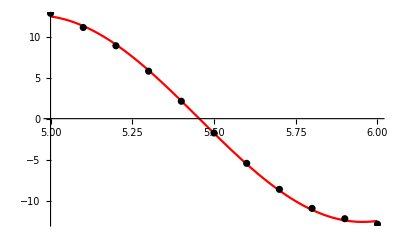

```mathematica
points = Table[{xt[[i]],z[[i]]},{i,1,n+1}];
grp = ListPlot[points,PlotStyle->Black];
grf = Plot[f'[x],{x,a,b}, PlotStyle->Red];
Show[grf, grp]
```

### Втора производна

попълваме вътрешните стойности

```mathematica
z = Table[(yt[[i-1]]-2yt[[i]]+yt[[i+1]])/h^2,{i,2,n}]
```

{-17.2335,-27.2545,-34.6077,-38.5732,-38.7629,-35.1583,-28.1121,-18.314,-6.72332}

добавяме последния елемент

добавяме първия елемент

#### Оценка на грешката

теоретична грешка

```mathematica
h^2
```

0.01

истинска грешка

```mathematica
z(*приближена стойност*)
```

{-17.2335,-27.2545,-34.6077,-38.5732,-38.7629,-35.1583,-28.1121,-18.314,-6.72332}

```mathematica
f''[xt](*истинска стойност*)
```

{-5.57119,-17.3759,-27.4798,-34.8938,-38.8921,-39.0833,-35.4489,-28.3444,-18.4654,-6.77889,5.57119}

```mathematica
Table[Abs[z[[i]]-f''[xt[[i+1]]]],{i,1,n-1}]
```

{0.142442,0.22527,0.286047,0.318824,0.320392,0.290598,0.232358,0.151373,0.0555711}

#### Визуализация

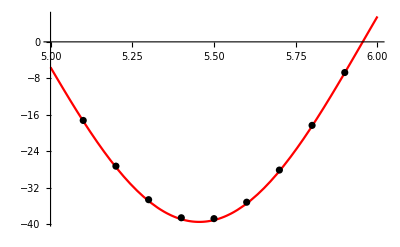

```mathematica
points = Table[{xt[[i+1]],z[[i]]},{i,1,n-1}];
grp = ListPlot[points,PlotStyle->Black];
grf = Plot[f''[x],{x,a,b}, PlotStyle->Red];
Show[grf, grp]
```

# Числено диференциране - увеличаване на точността чрез сгъстяване на мрежата

## Създаваме табличната функция

```mathematica
a =5.;b = 6;
n = 100;
h = (b-a)/n;
xt = Table[a + i*h,{i,0,n}]
```

{5.,5.01,5.02,5.03,5.04,5.05,5.06,5.07,5.08,5.09,5.1,5.11,5.12,5.13,5.14,5.15,5.16,5.17,5.18,5.19,5.2,5.21,5.22,5.23,5.24,5.25,5.26,5.27,5.28,5.29,5.3,5.31,5.32,5.33,5.34,5.35,5.36,5.37,5.38,5.39,5.4,5.41,5.42,5.43,5.44,5.45,5.46,5.47,5.48,5.49,5.5,5.51,5.52,5.53,5.54,5.55,5.56,5.57,5.58,5.59,5.6,5.61,5.62,5.63,5.64,5.65,5.66,5.67,5.68,5.69,5.7,5.71,5.72,5.73,5.74,5.75,5.76,5.77,5.78,5.79,5.8,5.81,5.82,5.83,5.84,5.85,5.86,5.87,5.88,5.89,5.9,5.91,5.92,5.93,5.94,5.95,5.96,5.97,5.98,5.99,6.}

```mathematica
Length[xt]
```

101

```mathematica
f[x_]:= 4 Sin[π x - 3]
yt =f[xt]
```

{0.56448,0.688587,0.812015,0.934641,1.05634,1.17701,1.29651,1.41473,1.53155,1.64686,1.76055,1.8725,1.9826,2.09075,2.19683,2.30074,2.40239,2.50166,2.59846,2.6927,2.78429,2.87312,2.95912,3.0422,3.12227,3.19927,3.27311,3.34371,3.41102,3.47496,3.53548,3.5925,3.64598,3.69586,3.74209,3.78463,3.82343,3.85846,3.88969,3.91707,3.94059,3.96022,3.97594,3.98774,3.9956,3.99952,3.99949,3.99552,3.9876,3.97575,3.95997,3.94029,3.91671,3.88927,3.858,3.82291,3.78406,3.74146,3.69518,3.64525,3.59172,3.53465,3.47409,3.4101,3.34274,3.27209,3.19821,3.12117,3.04105,2.95793,2.87189,2.78302,2.6914,2.59712,2.50028,2.40097,2.2993,2.19535,2.08924,1.98107,1.87094,1.75896,1.64525,1.52992,1.41307,1.29483,1.17532,1.05464,0.932922,0.810284,0.686846,0.56273,0.438059,0.312955,0.187543,0.0619454,-0.0637131,-0.189309,-0.314718,-0.439816,-0.56448}

## Намиране на производните с точност O(h) - първи порядък на грешката

### Първа производна

```mathematica
z = Table[(yt[[i+1]]-yt[[i]])/h,{i,1,n}]
```

{12.4107,12.3428,12.2626,12.1704,12.0661,11.95,11.822,11.6824,11.5313,11.3687,11.195,11.0102,10.8145,10.6082,10.3914,10.1644,9.92727,9.68039,9.42395,9.15821,8.88344,8.59989,8.30787,8.00764,7.69951,7.38378,7.06076,6.73078,6.39415,6.05121,5.7023,5.34777,4.98795,4.62322,4.25392,3.88042,3.50309,3.12231,2.73845,2.35188,1.96299,1.57216,1.17979,0.786245,0.391928,-0.00277685,-0.397478,-0.791788,-1.18532,-1.57767,-1.96848,-2.35733,-2.74387,-3.12769,-3.50843,-3.8857,-4.25914,-4.62838,-4.99305,-5.35279,-5.70725,-6.05608,-6.39893,-6.73547,-7.06535,-7.38827,-7.70389,-8.01192,-8.31203,-8.60394,-8.88736,-9.16201,-9.42762,-9.68393,-9.93067,-10.1676,-10.3945,-10.6112,-10.8174,-11.0129,-11.1975,-11.3711,-11.5335,-11.6845,-11.8239,-11.9517,-12.0677,-12.1718,-12.2638,-12.3438,-12.4116,-12.4671,-12.5103,-12.5412,-12.5597,-12.5659,-12.5596,-12.5409,-12.5098,-12.4664}

добавяме последния елемент

```mathematica
AppendTo[z, (yt[[n+1]]-yt[[n]])/h]
```

{12.4107,12.3428,12.2626,12.1704,12.0661,11.95,11.822,11.6824,11.5313,11.3687,11.195,11.0102,10.8145,10.6082,10.3914,10.1644,9.92727,9.68039,9.42395,9.15821,8.88344,8.59989,8.30787,8.00764,7.69951,7.38378,7.06076,6.73078,6.39415,6.05121,5.7023,5.34777,4.98795,4.62322,4.25392,3.88042,3.50309,3.12231,2.73845,2.35188,1.96299,1.57216,1.17979,0.786245,0.391928,-0.00277685,-0.397478,-0.791788,-1.18532,-1.57767,-1.96848,-2.35733,-2.74387,-3.12769,-3.50843,-3.8857,-4.25914,-4.62838,-4.99305,-5.35279,-5.70725,-6.05608,-6.39893,-6.73547,-7.06535,-7.38827,-7.70389,-8.01192,-8.31203,-8.60394,-8.88736,-9.16201,-9.42762,-9.68393,-9.93067,-10.1676,-10.3945,-10.6112,-10.8174,-11.0129,-11.1975,-11.3711,-11.5335,-11.6845,-11.8239,-11.9517,-12.0677,-12.1718,-12.2638,-12.3438,-12.4116,-12.4671,-12.5103,-12.5412,-12.5597,-12.5659,-12.5596,-12.5409,-12.5098,-12.4664,-12.4664}

#### Оценка на грешката

теоретична грешка

```mathematica
h
```

0.01

истинска грешка

```mathematica
z(*приближена стойност*)
```

{12.4107,12.3428,12.2626,12.1704,12.0661,11.95,11.822,11.6824,11.5313,11.3687,11.195,11.0102,10.8145,10.6082,10.3914,10.1644,9.92727,9.68039,9.42395,9.15821,8.88344,8.59989,8.30787,8.00764,7.69951,7.38378,7.06076,6.73078,6.39415,6.05121,5.7023,5.34777,4.98795,4.62322,4.25392,3.88042,3.50309,3.12231,2.73845,2.35188,1.96299,1.57216,1.17979,0.786245,0.391928,-0.00277685,-0.397478,-0.791788,-1.18532,-1.57767,-1.96848,-2.35733,-2.74387,-3.12769,-3.50843,-3.8857,-4.25914,-4.62838,-4.99305,-5.35279,-5.70725,-6.05608,-6.39893,-6.73547,-7.06535,-7.38827,-7.70389,-8.01192,-8.31203,-8.60394,-8.88736,-9.16201,-9.42762,-9.68393,-9.93067,-10.1676,-10.3945,-10.6112,-10.8174,-11.0129,-11.1975,-11.3711,-11.5335,-11.6845,-11.8239,-11.9517,-12.0677,-12.1718,-12.2638,-12.3438,-12.4116,-12.4671,-12.5103,-12.5412,-12.5597,-12.5659,-12.5596,-12.5409,-12.5098,-12.4664,-12.4664}

```mathematica
f'[xt](*истинска стойност*)
```

{12.4406,12.3788,12.3047,12.2185,12.1203,12.01,11.888,11.7542,11.6087,11.4519,11.2837,11.1044,10.9142,10.7131,10.5015,10.2796,10.0475,9.80544,9.55374,9.29261,9.02231,8.7431,8.45527,8.15909,7.85486,7.54288,7.22346,6.8969,6.56354,6.2237,5.87773,5.52594,5.16871,4.80638,4.4393,4.06784,3.69237,3.31325,2.93086,2.54558,2.15779,1.76787,1.3762,0.983178,0.589183,0.194607,-0.200161,-0.594731,-0.988714,-1.38172,-1.77337,-2.16326,-2.55102,-2.93626,-3.31861,-3.69767,-4.07309,-4.44449,-4.81151,-5.17377,-5.53093,-5.88263,-6.22853,-6.56828,-6.90155,-7.228,-7.54732,-7.8592,-8.16332,-8.45938,-8.74709,-9.02617,-9.29635,-9.55735,-9.80891,-10.0508,-10.2828,-10.5046,-10.716,-10.9169,-11.107,-11.2862,-11.4542,-11.6109,-11.7561,-11.8898,-12.0117,-12.1217,-12.2198,-12.3058,-12.3797,-12.4414,-12.4908,-12.5279,-12.5526,-12.5649,-12.5648,-12.5523,-12.5274,-12.4902,-12.4406}

```mathematica
Abs[z-f'[xt]]
```

{0.0299,0.0360137,0.042092,0.0481287,0.0541178,0.0600536,0.0659301,0.0717416,0.0774822,0.0831464,0.0887285,0.0942231,0.0996247,0.104928,0.110128,0.115219,0.120196,0.125055,0.12979,0.134397,0.138872,0.143209,0.147405,0.151456,0.155357,0.159105,0.162696,0.166127,0.169393,0.172492,0.175421,0.178177,0.180757,0.183159,0.18538,0.187418,0.189271,0.190937,0.192415,0.193702,0.194799,0.195704,0.196415,0.196933,0.197256,0.197384,0.197318,0.197057,0.196601,0.195952,0.195109,0.194073,0.192846,0.191429,0.189823,0.188029,0.18605,0.183888,0.181543,0.17902,0.17632,0.173446,0.170401,0.167187,0.163809,0.160269,0.156571,0.152718,0.148715,0.144565,0.140272,0.13584,0.131275,0.12658,0.12176,0.11682,0.111765,0.1066,0.101329,0.095958,0.0904926,0.0849378,0.0792992,0.0735824,0.0677929,0.0619365,0.056019,0.0500463,0.0440241,0.0379585,0.0318554,0.0257209,0.019561,0.0133818,0.0071894,0.000989898,0.00521058,0.0114059,0.01759,0.0237567,0.0258074}

#### Визуализация

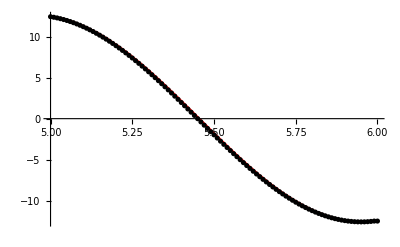

```mathematica
points = Table[{xt[[i]],z[[i]]},{i,1,n+1}];
grp = ListPlot[points,PlotStyle->Black];
grf = Plot[f'[x],{x,a,b}, PlotStyle->Red];
Show[grf, grp]
```

## Намиране на производните с точност O(h^2) - втори порядък на грешката

### Първа производна

попълваме вътрешните стойности

```mathematica
z = Table[(yt[[i+1]]-yt[[i-1]])/(2h),{i,2,n}]
```

{12.3767,12.3027,12.2165,12.1183,12.0081,11.886,11.7522,11.6068,11.45,11.2819,11.1026,10.9124,10.7114,10.4998,10.2779,10.0458,9.80383,9.55217,9.29108,9.02082,8.74167,8.45388,8.15775,7.85357,7.54164,7.22227,6.89577,6.56246,6.22268,5.87676,5.52504,5.16786,4.80559,4.43857,4.06717,3.69176,3.3127,2.93038,2.54516,2.15743,1.76758,1.37598,0.983016,0.589086,0.194575,-0.200128,-0.594633,-0.988552,-1.38149,-1.77307,-2.1629,-2.5506,-2.93578,-3.31806,-3.69707,-4.07242,-4.44376,-4.81072,-5.17292,-5.53002,-5.88167,-6.2275,-6.5672,-6.90041,-7.22681,-7.54608,-7.85791,-8.16197,-8.45799,-8.74565,-9.02469,-9.29482,-9.55577,-9.8073,-10.0491,-10.2811,-10.5029,-10.7143,-10.9151,-11.1052,-11.2843,-11.4523,-11.609,-11.7542,-11.8878,-12.0097,-12.1197,-12.2178,-12.3038,-12.3777,-12.4393,-12.4887,-12.5258,-12.5505,-12.5628,-12.5627,-12.5502,-12.5254,-12.4881}

добавяме последния елемент

```mathematica
AppendTo[z, (yt[[n-1]]-4yt[[n]]+3yt[[n+1]])/(2h)]
```

{12.3767,12.3027,12.2165,12.1183,12.0081,11.886,11.7522,11.6068,11.45,11.2819,11.1026,10.9124,10.7114,10.4998,10.2779,10.0458,9.80383,9.55217,9.29108,9.02082,8.74167,8.45388,8.15775,7.85357,7.54164,7.22227,6.89577,6.56246,6.22268,5.87676,5.52504,5.16786,4.80559,4.43857,4.06717,3.69176,3.3127,2.93038,2.54516,2.15743,1.76758,1.37598,0.983016,0.589086,0.194575,-0.200128,-0.594633,-0.988552,-1.38149,-1.77307,-2.1629,-2.5506,-2.93578,-3.31806,-3.69707,-4.07242,-4.44376,-4.81072,-5.17292,-5.53002,-5.88167,-6.2275,-6.5672,-6.90041,-7.22681,-7.54608,-7.85791,-8.16197,-8.45799,-8.74565,-9.02469,-9.29482,-9.55577,-9.8073,-10.0491,-10.2811,-10.5029,-10.7143,-10.9151,-11.1052,-11.2843,-11.4523,-11.609,-11.7542,-11.8878,-12.0097,-12.1197,-12.2178,-12.3038,-12.3777,-12.4393,-12.4887,-12.5258,-12.5505,-12.5628,-12.5627,-12.5502,-12.5254,-12.4881,-12.4447}

добавяме първия елемент

```mathematica
PrependTo[z, (-3yt[[1]]+4yt[[2]]-yt[[3]])/(2h)]
```

{12.4447,12.3767,12.3027,12.2165,12.1183,12.0081,11.886,11.7522,11.6068,11.45,11.2819,11.1026,10.9124,10.7114,10.4998,10.2779,10.0458,9.80383,9.55217,9.29108,9.02082,8.74167,8.45388,8.15775,7.85357,7.54164,7.22227,6.89577,6.56246,6.22268,5.87676,5.52504,5.16786,4.80559,4.43857,4.06717,3.69176,3.3127,2.93038,2.54516,2.15743,1.76758,1.37598,0.983016,0.589086,0.194575,-0.200128,-0.594633,-0.988552,-1.38149,-1.77307,-2.1629,-2.5506,-2.93578,-3.31806,-3.69707,-4.07242,-4.44376,-4.81072,-5.17292,-5.53002,-5.88167,-6.2275,-6.5672,-6.90041,-7.22681,-7.54608,-7.85791,-8.16197,-8.45799,-8.74565,-9.02469,-9.29482,-9.55577,-9.8073,-10.0491,-10.2811,-10.5029,-10.7143,-10.9151,-11.1052,-11.2843,-11.4523,-11.609,-11.7542,-11.8878,-12.0097,-12.1197,-12.2178,-12.3038,-12.3777,-12.4393,-12.4887,-12.5258,-12.5505,-12.5628,-12.5627,-12.5502,-12.5254,-12.4881,-12.4447}

#### Оценка на грешката

теоретична грешка

```mathematica
h^2
```

0.0001

истинска грешка

```mathematica
z(*приближена стойност*)
```

{12.4447,12.3767,12.3027,12.2165,12.1183,12.0081,11.886,11.7522,11.6068,11.45,11.2819,11.1026,10.9124,10.7114,10.4998,10.2779,10.0458,9.80383,9.55217,9.29108,9.02082,8.74167,8.45388,8.15775,7.85357,7.54164,7.22227,6.89577,6.56246,6.22268,5.87676,5.52504,5.16786,4.80559,4.43857,4.06717,3.69176,3.3127,2.93038,2.54516,2.15743,1.76758,1.37598,0.983016,0.589086,0.194575,-0.200128,-0.594633,-0.988552,-1.38149,-1.77307,-2.1629,-2.5506,-2.93578,-3.31806,-3.69707,-4.07242,-4.44376,-4.81072,-5.17292,-5.53002,-5.88167,-6.2275,-6.5672,-6.90041,-7.22681,-7.54608,-7.85791,-8.16197,-8.45799,-8.74565,-9.02469,-9.29482,-9.55577,-9.8073,-10.0491,-10.2811,-10.5029,-10.7143,-10.9151,-11.1052,-11.2843,-11.4523,-11.609,-11.7542,-11.8878,-12.0097,-12.1197,-12.2178,-12.3038,-12.3777,-12.4393,-12.4887,-12.5258,-12.5505,-12.5628,-12.5627,-12.5502,-12.5254,-12.4881,-12.4447}

```mathematica
f'[xt](*истинска стойност*)
```

{12.4406,12.3788,12.3047,12.2185,12.1203,12.01,11.888,11.7542,11.6087,11.4519,11.2837,11.1044,10.9142,10.7131,10.5015,10.2796,10.0475,9.80544,9.55374,9.29261,9.02231,8.7431,8.45527,8.15909,7.85486,7.54288,7.22346,6.8969,6.56354,6.2237,5.87773,5.52594,5.16871,4.80638,4.4393,4.06784,3.69237,3.31325,2.93086,2.54558,2.15779,1.76787,1.3762,0.983178,0.589183,0.194607,-0.200161,-0.594731,-0.988714,-1.38172,-1.77337,-2.16326,-2.55102,-2.93626,-3.31861,-3.69767,-4.07309,-4.44449,-4.81151,-5.17377,-5.53093,-5.88263,-6.22853,-6.56828,-6.90155,-7.228,-7.54732,-7.8592,-8.16332,-8.45938,-8.74709,-9.02617,-9.29635,-9.55735,-9.80891,-10.0508,-10.2828,-10.5046,-10.716,-10.9169,-11.107,-11.2862,-11.4542,-11.6109,-11.7561,-11.8898,-12.0117,-12.1217,-12.2198,-12.3058,-12.3797,-12.4414,-12.4908,-12.5279,-12.5526,-12.5649,-12.5648,-12.5523,-12.5274,-12.4902,-12.4406}

```mathematica
Abs[z-f'[xt]]
```

{0.00407764,0.00203613,0.00202394,0.00200977,0.0019936,0.00197547,0.00195539,0.00193339,0.00190947,0.00188367,0.00185601,0.00182651,0.00179522,0.00176215,0.00172735,0.00169084,0.00165266,0.00161285,0.00157145,0.0015285,0.00148404,0.00143811,0.00139077,0.00134205,0.00129201,0.00124069,0.00118815,0.00113444,0.00107961,0.00102371,0.000966799,0.000908937,0.000850177,0.000790578,0.000730199,0.0006691,0.00060734,0.000544981,0.000482083,0.000418711,0.000354925,0.000290788,0.000226365,0.000161718,0.000096912,0.00003201,0.0000329235,0.0000978245,0.000162629,0.000227273,0.000291693,0.000355825,0.000419605,0.000482972,0.000545862,0.000608213,0.000669964,0.000731054,0.000791422,0.00085101,0.000909757,0.000967607,0.0010245,0.00108039,0.0011352,0.0011889,0.00124142,0.00129272,0.00134275,0.00139144,0.00143877,0.00148467,0.00152911,0.00157204,0.00161342,0.00165321,0.00169136,0.00172785,0.00176263,0.00179567,0.00182694,0.00185641,0.00188404,0.00190982,0.00193371,0.00195569,0.00197574,0.00199384,0.00200998,0.00202413,0.00203628,0.00204643,0.00205455,0.00206065,0.00206471,0.00206674,0.00206672,0.00206467,0.00206058,0.00205445,0.00410513}

#### Визуализация

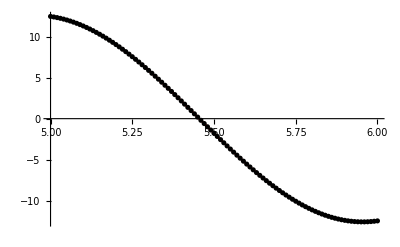

```mathematica
points = Table[{xt[[i]],z[[i]]},{i,1,n+1}];
grp = ListPlot[points,PlotStyle->Black];
grf = Plot[f'[x],{x,a,b}, PlotStyle->Red];
Show[grf, grp]
```

### Втора производна

попълваме вътрешните стойности

```mathematica
z = Table[(yt[[i-1]]-2yt[[i]]+yt[[i+1]])/h^2,{i,2,n}]
```

{-6.79552,-8.01361,-9.22378,-10.4248,-11.6156,-12.7949,-13.9616,-15.1146,-16.2525,-17.3745,-18.4793,-19.5659,-20.6332,-21.6801,-22.7056,-23.7087,-24.6884,-25.6437,-26.5737,-27.4775,-28.3542,-29.2029,-30.0228,-30.8131,-31.5729,-32.3016,-32.9984,-33.6627,-34.2937,-34.8909,-35.4536,-35.9814,-36.4736,-36.9299,-37.3497,-37.7327,-38.0784,-38.3865,-38.6568,-38.8889,-39.0826,-39.2377,-39.3542,-39.4318,-39.4704,-39.4702,-39.4309,-39.3528,-39.2358,-39.0801,-38.8859,-38.6532,-38.3824,-38.0738,-37.7275,-37.3441,-36.9237,-36.467,-35.9742,-35.446,-34.8827,-34.2851,-33.6536,-32.9888,-32.2916,-31.5624,-30.8022,-30.0115,-29.1912,-28.3421,-27.465,-26.5608,-25.6304,-24.6748,-23.6947,-22.6913,-21.6655,-20.6183,-19.5507,-18.4639,-17.3588,-16.2366,-15.0984,-13.9453,-12.7784,-11.599,-10.408,-9.20681,-7.99652,-6.77834,-5.55346,-4.32311,-3.08849,-1.85082,-0.611327,0.628771,1.86825,3.10588,4.34045}

добавяме последния елемент

добавяме първия елемент

#### Оценка на грешката

теоретична грешка

```mathematica
h^2
```

0.0001

истинска грешка

```mathematica
z(*приближена стойност*)
```

{-6.79552,-8.01361,-9.22378,-10.4248,-11.6156,-12.7949,-13.9616,-15.1146,-16.2525,-17.3745,-18.4793,-19.5659,-20.6332,-21.6801,-22.7056,-23.7087,-24.6884,-25.6437,-26.5737,-27.4775,-28.3542,-29.2029,-30.0228,-30.8131,-31.5729,-32.3016,-32.9984,-33.6627,-34.2937,-34.8909,-35.4536,-35.9814,-36.4736,-36.9299,-37.3497,-37.7327,-38.0784,-38.3865,-38.6568,-38.8889,-39.0826,-39.2377,-39.3542,-39.4318,-39.4704,-39.4702,-39.4309,-39.3528,-39.2358,-39.0801,-38.8859,-38.6532,-38.3824,-38.0738,-37.7275,-37.3441,-36.9237,-36.467,-35.9742,-35.446,-34.8827,-34.2851,-33.6536,-32.9888,-32.2916,-31.5624,-30.8022,-30.0115,-29.1912,-28.3421,-27.465,-26.5608,-25.6304,-24.6748,-23.6947,-22.6913,-21.6655,-20.6183,-19.5507,-18.4639,-17.3588,-16.2366,-15.0984,-13.9453,-12.7784,-11.599,-10.408,-9.20681,-7.99652,-6.77834,-5.55346,-4.32311,-3.08849,-1.85082,-0.611327,0.628771,1.86825,3.10588,4.34045}

```mathematica
f''[xt](*истинска стойност*)
```

{-5.57119,-6.79608,-8.01426,-9.22454,-10.4257,-11.6166,-12.796,-13.9628,-15.1158,-16.2539,-17.3759,-18.4808,-19.5675,-20.6349,-21.6818,-22.7074,-23.7106,-24.6904,-25.6458,-26.5759,-27.4798,-28.3566,-29.2053,-30.0253,-30.8156,-31.5755,-32.3043,-33.0011,-33.6654,-34.2965,-34.8938,-35.4565,-35.9843,-36.4766,-36.9329,-37.3528,-37.7358,-38.0815,-38.3897,-38.6599,-38.8921,-39.0858,-39.241,-39.3574,-39.435,-39.4737,-39.4734,-39.4342,-39.356,-39.239,-39.0833,-38.8891,-38.6564,-38.3856,-38.0769,-37.7306,-37.3471,-36.9268,-36.47,-35.9772,-35.4489,-34.8856,-34.2879,-33.6563,-32.9916,-32.2942,-31.565,-30.8047,-30.014,-29.1936,-28.3444,-27.4673,-26.563,-25.6325,-24.6768,-23.6967,-22.6932,-21.6673,-20.62,-19.5523,-18.4654,-17.3603,-16.238,-15.0997,-13.9465,-12.7795,-11.5999,-10.4089,-9.20757,-7.99718,-6.77889,-5.55392,-4.32347,-3.08874,-1.85097,-0.611377,0.628823,1.8684,3.10614,4.34081,5.57119}

```mathematica
Table[Abs[z[[i]]-f''[xt[[i+1]]]],{i,1,n-1}]
```

{0.000558937,0.000659125,0.000758663,0.000857452,0.000955394,0.00105239,0.00114836,0.00124318,0.00133678,0.00142907,0.00151994,0.00160931,0.00169709,0.0017832,0.00186755,0.00195006,0.00203064,0.00210921,0.00218571,0.00226005,0.00233216,0.00240196,0.0024694,0.0025344,0.0025969,0.00265683,0.00271415,0.00276878,0.00282068,0.0028698,0.00291609,0.0029595,0.00299998,0.00303751,0.00307204,0.00310354,0.00313197,0.00315732,0.00317955,0.00319864,0.00321457,0.00322733,0.00323691,0.00324329,0.00324647,0.00324645,0.00324322,0.0032368,0.00322718,0.00321437,0.00319839,0.00317926,0.00315698,0.0031316,0.00310312,0.00307158,0.003037,0.00299944,0.00295891,0.00291546,0.00286913,0.00281997,0.00276803,0.00271336,0.00265601,0.00259604,0.0025335,0.00246847,0.002401,0.00233116,0.00225902,0.00218465,0.00210812,0.00202952,0.00194891,0.00186638,0.001782,0.00169587,0.00160806,0.00151867,0.00142778,0.00133548,0.00124186,0.00114701,0.00105104,0.000954023,0.000856068,0.000757267,0.00065772,0.000557524,0.000456776,0.000355579,0.00025403,0.000152232,0.0000502819,0.0000517168,0.000153665,0.000255461,0.000357005}

#### Визуализация

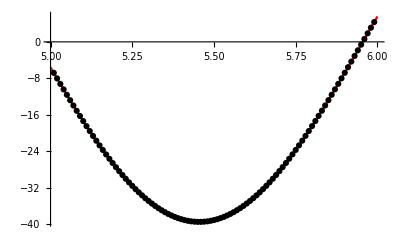

```mathematica
points = Table[{xt[[i+1]],z[[i]]},{i,1,n-1}];
grp = ListPlot[points,PlotStyle->Black];
grf = Plot[f''[x],{x,a,b}, PlotStyle->Red];
Show[grf, grp]
```